# WoAm Collision

Features:

2 Dimensions - 3 Dimensions
Axis Aligned Bounding Box - Oriented Bounding Box
Solve - Render
Point, segment, polygon, sphere

// GO FURTHER: line
// GO FURTHER: render, be ready against possible bugs because point {3.12, 4.02} is displayed on the screen at {3, 4} 
// GO FURTHER: draw, draw and DRAW ! (pictures)
// GO FURTHER: optimize computation (check the definition field, the height range...)
// GO FURTHER: use manipulate to see collision happen
// GO FURTHER: manage the collision (go back in time, go to the collision point...)
// GO FURTHER: render with red at the collision area

Theory of collisions (mathematic formulas) found on a french website: https://openclassrooms.com/courses/theorie-des-collisions

## 2D

API

We use the gamma’s rule, if the determinant computed is greater than or equal to zero so the point is left to the segment (or in the segment)
D: vector from sP0 to sP1 (vectors variables are written in upper case)
T: vector from sP0 to p
d: determinant

```mathematica
computeDeterminant[p_,sP0_,sP1_]:=
Module[{D,T, d},
D={sP1[[1]]-sP0[[1]], (* D = {sP1X - sP0X, *)
sP1[[2]]-sP0[[2]]}; (*       sP1Y - sP0Y} *)
T={p[[1]]-sP0[[1]], (* T = {pX - sP0X, *)
p[[2]]-sP0[[2]]}; (*       pY - sP0Y} *)
d=D[[1]] T[[2]]-D[[2]] T[[1]]; (* DX * TY - DY * TX *)
Return[d];]
```

Point in another point (AABB - AABB)

p: point

```mathematica
isPointInAnotherPoint2D[p0_,p1_]:=
If[p0[[1]]==p1[[1]]&&p0[[2]]==p1[[2]],True,False] (* Just check if coordinates of both points are the same *)
```

Point in a segment (AABB - AABB/OBB)

Points of the segment must be given in the followed order: left, right

The affine function which draws the segment is: ax + b = 0
a: the leading coefficient of the function
x: the unknown
b: the height at the origin

s: segment, sPX: point x of a segment

```mathematica
isPointInASegment2D[p_,sP0_,sP1_]:=
If[sP0[[1]]≤p[[1]]≤sP1[[1]],(* Check if pX is in the definition field of the segment *)
If[sP0[[2]]≤p[[2]]≤sP1[[2]] || sP1 [[2]]≤ p[[2]] ≤ sP0[[2]],(* Check if pY is in the height range of the segment *)
Module[{a,b,yCmptd,xCmptd},
yCmptd=sP1[[2]]-sP0[[2]];
If[yCmptd==0,Return[True]]; (* Check if we are in the limit case of point in a segment which is included in the y-axis *)
xCmptd=sP1[[1]]-sP0[[1]];
If[xCmptd==0,Return[True]];(* Check if we are in the limit case of point in a segment which is included in the x-axis *)
a=yCmptd/xCmptd; (* Assign the leading coefficient of the function to a computed with (sP1Y - sP0Y)/(sP1X - sP0X) *)
b=Solve[a sP0[[1]]+b==sP0[[2]],b][[All,1,2]][[1]]; (* Assign the solution of a * sP0X + b == sP0Y to b which is the height at the origin *)
If[a p[[1]]+b==p[[2]],True,False]] (* Check if the applying of the function match with p coordinates, by using the equation a * pX + b == pY *)
,False] (* To optimize we first check the definition field and height range of the segment to reduce the computation time and return False if it doesn't match *)
,False]

isPointInASegment2D[{1,1},{0,0},{3,3}]
```

True

Point in a polygon (AABB - OBB)

Points of the polygon must be given in the followed order:

Example for a triangle:

- top, bottom-left, bottom-right or
- bottom-left, bottom-right, top or
- bottom-right, top, bottom-left (we need to “turn left” at each angle)

-Graphics-

Example for a quadrilateral:

- top-left, bottom-left, bottom-right, top-right or
- bottom-left, bottom-right, top-right, top-left or
- bottom-right, top-right, top-left, bottom-left or
- top-right, top-left, bottom-left, bottom-right (we need to “turn left” at each angle)

-Graphics-

Here we use our API

l: list of geometric objects

```mathematica
isPointInAPolygon2D[p_,l_]:=
Module[{lLngth}, (* lLngth is the length of the list l *)
lLngth=Length[l];
For[i=1,i<=lLngth,i++, (* For each point of the list l *)
If[computeDeterminant[p,l[[i]],l[[i+1]]]≥0, (* We compute the determinant of the segment defined by two followed points *)
If[i==lLngth-1, (* Check if we are not at the lLngth - 1 element *)
If[computeDeterminant[p,l[[lLngth]],l[[1]]]≥0, (* Otherwise the followed point is the first of the list l *)
Return[True],(* If the determinant is greater or equal to zero we return True *)
Return[False]]],(* Otherwise we return False *)
Return[False]]]] (* Same as two comments above (but here we are in the common If) *)
```

Point in a quadrilateral (AABB - AABB)

q: quadrilateral

-Graphics-

```mathematica
isPointInAQuadrilateralAABB2D[p_,qP0_,qP1_,qP2_,qP3_]:=
If[qP1[[1]]≤p[[1]]≤qP2[[1]], (* Check if pX is in the definition field of the quadrilateral *)
If[qP1[[2]]≤p[[2]]≤qP0[[2]],True,False], (* Check if pY is in the height range of the quadrilateral *)
False]
```

Point in a disk (AABB - OBB)

The distance between the given point and the center of the disk is: √((pX-cX)^2+(pY-cY)^2)
d: disk {cX, cY, r}
c: center
r: radius

```mathematica
isPointInADisk2D[p_,d_]:=
If[√((p[[1]]-d[[1]])^2+(p[[2]]-d[[2]])^2)≤d[[3]],True,False] (* Check if the distance between the given point and the center of the disk is less or equal to the disk radius *)
```

Line hits a segment (AABB/OBB - AABB/OBB)

li: line
LI: vector from liP0 to liP1
LIS0: vector from sP0 to liP0
LIS1: vector from sP1 to liP0
// GO FURTHER: check if the order is important

Here we don’t use our API to compute the determinant

```mathematica
isLineHittingASegment[liP0_,liP1_,sP0_,sP1_]:=
Module[{LI,LIS0,LIS1}, (* For local variables we use one bracket to patch the bug that we can't (or we don't know how to do) make a local list, so a function matches too with our requirements *)
LI[1]=liP1[[1]]-liP0[[1]]; (* LIX = liP1X - liP0X *)
LI[2]=liP1[[2]]-liP0[[2]]; (* LIY = liP1Y - liP0Y *)
LIS0[1]=sP0[[1]]-liP0[[1]];(* LIS0X = sP0X - liP0X *)
LIS0[2]=sP0[[2]]-liP0[[2]];(* LIS0Y = sP0Y - liP0Y *)
LIS1[1]=sP1[[1]]-liP0[[1]];(* LIS1X = sP1X - liP0X *)
LIS1[2]=sP1[[2]]-liP0[[2]];(* LIS1Y = sP1Y - liP0Y *)
If[(LI[1]*LIS1[2]-LI[2]*LIS1[1])*(LI[1]*LIS0[2]-LI[2]*LIS0[1])≤0, (* Check if the multiplication between the determinants return a negative value, in this case sP0 and sP1 are not in the same side delimited by the line *)
Return[True],Return[False]];] (* If we are in this case, the segment must hit the line like in the draw below *)
```

Segment hits a segment (AABB/OBB - AABB/OBB)

Here we use the function isLineHittingASegment defined above

```mathematica
isSegmentHittingASegment[sP0_,sP1_,sP2_,sP3_]:=
If[isLineHittingASegment[sP0,sP1,sP2,sP3]==False,Return[False],(* Check if both points of the segment are in the same side delimited by the line, if this case is completed (the function returns False) and it is very easy to see that we can stop searching an intersection between the line and the segment *)
If[isLineHittingASegment[sP2,sP3,sP0,sP1]==False,Return[False],Return[True]]]; (* Check if the case that if the function isLineHittingASegment with both points of the segment which delimits a line in first arguments returns False, in this case there is no contact between the segment and the line *)
```

```mathematica
isSegmentHittingASegment[{0,0},{0,1},{0,-1},{0,-.1}] (* limit case <- to patch *)
```

True

Line hits a disk (AABB/OBB - OBB)

LI: vector from liP0 to liP1
LID: vector from liP0 to the center of the disk d

```mathematica
isLineHittingADisk[liP0_,liP1_,d_]:=
Module[{LI,LID,numerator,denominator},
LI[1]=liP1[[1]]-liP0[[1]]; (* LIX = liP1X - liP0X *)
LI[2]=liP1[[2]]-liP0[[2]]; (* LIY = liP1Y - liP0Y *)
LID[1]=d[[1]]-liP0[[1]]; (* LIDX = dX - liP0X *)
LID[2]=d[[2]]-liP0[[2]]; (* LIDY = dY - liP0Y *)
numerator=Abs[LI[1]*LID[2]-LI[2]*LID[1]]; (* Norm of the vector of the cross product of LI and LID, we use the function Abs (absolute) because a length can't be less than zero *)
denominator=√(LI[1]^2+LI[2]^2);(* Norm of the vector LI *)
If[numerator/denominator≤d[[2]],Return[True],Return[False]]] (* Check if the length of the orthogonal projection of the center of the disk on the line is less or equal to the radius of the disk *)
```

```mathematica
isLineHittingADisk[{2,1},{2,2},{1,1,0.5}] // BRUH
```

True

Render

l: list of geometric objects

```mathematica
render2D[l_]:=
If[IntegerQ[l[[1]]], (* Check if l is a basic list of integers *) (* TODO: segment and think about p + s + s +p + s + ... *)
Graphics[Point[{l[[1]],l[[2]]}],Frame->True], (* If True, we draw this point *)
Graphics[Point[l],Frame->True]] (* If False, we draw all the points of the list l *)
```

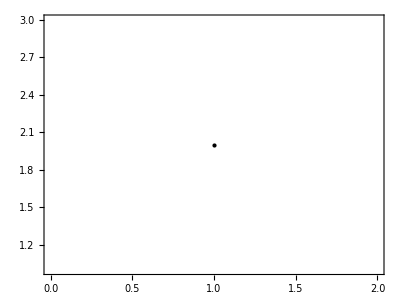

```mathematica
render2D[{1,2}]
```

## 3D

Render